# Hyperfine Structure

```mathematica
h=4.135668×10^-15;(*in eVs*)
```

## Etalon

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
xpeak={0.000342985,0.00073219,0.00111655,0.00149441,0.00185836}*10^3(*in ms*)
sxpeak={1.488*10^-7,1.476*10^-7,1.283*10^-7,1.409*10^-7,1.441*10^-7}*10^3;
fsr=9924.0 ;(*Freier Spektralbereich in  MHz*)
sfsr=30;
```

{0.342985,0.73219,1.11655,1.49441,1.85836}

```mathematica
dx=Table[xpeak[[i]]-xpeak[[3]],{i,1,5}];
```

```mathematica
sdx=Table[Sqrt[sxpeak[[3]]^2+sxpeak[[i]]^2],{i,1,5}];
```

```mathematica
xmodel=LinearModelFit[xpeak,x,x,Weights->1/sxpeak^2];
```

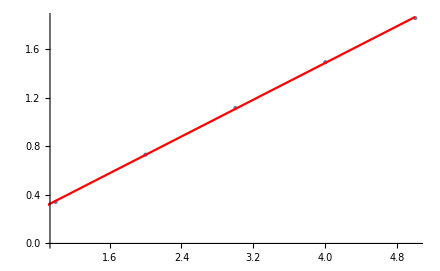

```mathematica
Show[ErrorListPlot[Transpose[{xpeak,sxpeak}],PlotStyle-> PointSize[Tiny]],Plot[xmodel["BestFit"],{x,0,5},PlotStyle-> Red]]
```

```mathematica
xmodel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0282967 | 0.00981288 | -2.88362 | 0.0633414
x | 0.379234 | 0.00294185 | 128.91 | 1.02924×10^-6

```mathematica
b=fsr/xmodel["BestFitParameters"][[2]]
sb=b*Sqrt[(sfsr/fsr)^2+(xmodel["ParameterTableEntries"][[2]][[2]]/xmodel["BestFitParameters"][[2]])^2]
```

26168.5

217.868

## Identifying peaks

```mathematica
hfs={0.000104108828673302,0.000128883133318368,0.000215125241268236,0.000339898243152262,0.000370754338634273,0.00039892544798297};
```

```mathematica
shfs={1.76425915159248*10^-7,9.21704289039901*10^-7,4.57855114799512*10^-8,2.866372961913589*10^-8,6.20690752304209*10^-8,5.65198359268252*10^-8};
```

```mathematica
(*third peak is reference peak*)
dhfs=Table[hfs[[i]]-hfs[[3]],{i,1,6}]*10^3 (*in ms*)
```

{-0.111016,-0.0862421,0.,0.124773,0.155629,0.1838}

```mathematica
sdhfs=Table[Sqrt[shfs[[i]]^2+shfs[[3]]^2],{i,1,6}]
```

{1.8227×10^-7,9.22841×10^-7,6.47505×10^-8,5.40178×10^-8,7.7129×10^-8,7.27379×10^-8}

```mathematica
δhfs=dhfs*b;
δhfs=Reverse[δhfs](* now in correct order *)
sδhfs= Sqrt[(b*sdhfs)^2+(dhfs*sb)^2];
sδhfs=Reverse[sδhfs]
```

{4809.78,4072.59,3265.13,0.,-2256.83,-2905.14}

{40.0441,33.9066,27.184,0.00169443,18.7894,24.1869}

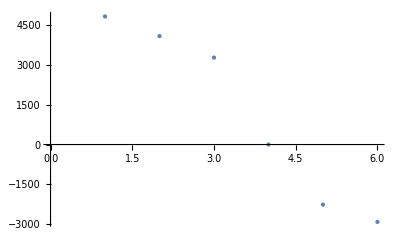

-Graphics-

```mathematica
ErrorListPlot[Transpose[{δhfs,sδhfs}],PlotStyle->PointSize[Tiny]]
```

## HFS constant A

Rubidium 87

## ^2 P_(1/2)

```mathematica
Ap2=h*(δhfs[[1]]-δhfs[[2]])*10^6 /2(*10^6 wegen MHz, int nach Ap gibt F des Ausgangszustandes,den beiden Linien gemeinsam haben*)
```

1.5244×10^-6

```mathematica
sAp2= h*Sqrt[sδhfs[[1]]^2+sδhfs[[2]]^2]*10^6 /2
```

1.08501×10^-7

```mathematica
Ap1=h*(δhfs[[5]]-δhfs[[6]])/2*10^6(*in eV*)
```

1.34059×10^-6

```mathematica
sAp1= h*Sqrt[sδhfs[[5]]^2+sδhfs[[6]]^2]*10^6 /2
```

6.33327×10^-8

```mathematica
sδhfs
```

{40.0441,33.9066,27.184,0.00169443,18.7894,24.1869}

## ^2 S_(1/2)

```mathematica
As1=h*(δhfs[[1]]-δhfs[[5]])/2*10^6 (*int nach As nun F des Endzustandes*)
```

0.0000146126

```mathematica
sAs1= h*Sqrt[sδhfs[[1]]^2+sδhfs[[5]]^2]*10^6 /2
```

9.14669×10^-8

```mathematica
As2=h*(δhfs[[2]]-δhfs[[6]])/2*10^6
```

0.0000144288

```mathematica
sAs2= h*Sqrt[sδhfs[[2]]^2+sδhfs[[6]]^2]*10^6 /2
```

8.61238×10^-8

Rubidium 85

## ^2 P_(1/2)

benötigte peaks nicht auflösbar

## ^2 S_(1/2)

```mathematica
A3=h*(δhfs[[3]]-δhfs[[4]])/3*10^6
```

4.50116×10^-6

```mathematica
sA3=h*Sqrt[sδhfs[[3]]^2+sδhfs[[4]]^2]/3*10^6
```

3.74747×10^-8